```mathematica
zt4[l_] := Product[(1-1/(ZetaZero[r]+2))(1-1/(ZetaZero[-r]+2)),{r,1,l}]
N[zt4[1,800]]
```

1.-3.33067×10^-16 ⅈ

```mathematica
F1[b_,c_]:=(1+(1-2 (1/2-c))/((1/2-c)^2+b^2))
F2[b_,c_]:=(1+(1-2 (1/2+c))/((1/2+c)^2+b^2))
```

```mathematica
F1[1,1/7]
```

277/221

```mathematica
F2[1,1/7]
```

221/277

```mathematica
FullSimplify[(1-1/(a+b I))(1-1/(a-b I))]
```

1+(1-2 a)/(a^2+b^2)

```mathematica
FullSimplify[(1-2/(a+b I))(1-2/(a-b I))]
```

1+(4-4 a)/(a^2+b^2)

```mathematica
(1+(4-4 (1/2-c))/((1/2-c)^2+b^2))(1+(4-4 (1/2+c))/((1/2+c)^2+b^2))
```

```mathematica
Expand[(1+(4-4 (1/2-c))/(b^2+(1/2-c)^2)) (1+(4-4 (1/2+c))/(b^2+(1/2+c)^2))]
```

```mathematica
FullSimplify[1+2/(b^2+(1/2-c)^2)+(4 c)/(b^2+(1/2-c)^2)+2/(b^2+(1/2+c)^2)+4/((b^2+(1/2-c)^2) (b^2+(1/2+c)^2))-(4 c)/(b^2+(1/2+c)^2)-(16 c^2)/((b^2+(1/2-c)^2) (b^2+(1/2+c)^2))]
```

```mathematica
ff[b_,c_]:=(16 b^4+(9-4 c^2)^2+8 b^2 (9+4 c^2))/((1+4 b^2)^2+8 (-1+4 b^2) c^2+16 c^4)
```

```mathematica
ff[0,c]
```

((9-4 c^2)^2)/(1-8 c^2+16 c^4)

```mathematica
ff[1/4,c]
```

(1/16+(9-4 c^2)^2+1/2 (9+4 c^2))/(25/16-6 c^2+16 c^4)

```mathematica
ff[1/2,c]
```

(1+(9-4 c^2)^2+2 (9+4 c^2))/(4+16 c^4)

```mathematica
N[Table[{n,ff[s,15]},{s,0,1/2,1/20}]//TableForm]
```

n | 0.982282
n | 0.982282
n | 0.982284
n | 0.982287
n | 0.982291
n | 0.982296
n | 0.982303
n | 0.982311
n | 0.98232
n | 0.98233
n | 0.982341

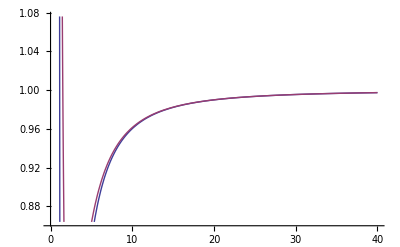

```mathematica
Plot[ {ff[0,c],ff[1,c]},{c,0,40}]
```

```mathematica
zt4[l_] := Product[(1-1/ZetaZero[r])(1-1/ZetaZero[-r]),{r,1,l}]
N[zt4[1,800]]
```

```mathematica
0.9999999999999956-3.3306690738754696*^-16 ⅈ
```

```mathematica
zt4a[l_] := Sum[Log[1-1/ZetaZero[r]]+Log[1-1/ZetaZero[-r]],{r,1,l}]
N[zt4a[100]]
```

-8.81897×10^-17+0. ⅈ

```mathematica
N[Log[1-1/ZetaZero[1]]+Log[1-1/ZetaZero[-1]]]
```

-4.42354×10^-17+0. ⅈ

```mathematica
N[Log[1-1/(.5+3I)]+Log[1-1/(.5-3I)]]
```

0.+0. ⅈ

```mathematica
N[Log[1-1/(.5+3I)]]
```

0.+0.330297 ⅈ

```mathematica
N[Log[1-1/(.3+3I)]+Log[1-1/(.3-3I)]]
```

0.0430637+0. ⅈ

```mathematica
N[Log[1-1/(.7+3I)]+Log[1-1/(.7-3I)]]
```

-0.0430637+0. ⅈ

```mathematica
FullSimplify[(1+1/(a+b I))(1+1/(a-b I))]
```

```mathematica
(1+(1+2 (1/2-c))/((1/2-c)^2+b^2))(1+(1+2 (1/2+c))/((1/2+c)^2+b^2))
```

```mathematica
FullSimplify[Expand[(1+(1+2 (1/2-c))/(b^2+(1/2-c)^2)) (1+(1+2 (1/2+c))/(b^2+(1/2+c)^2))]]
```

(16 b^4+(9-4 c^2)^2+8 b^2 (9+4 c^2))/((1+4 b^2)^2+8 (-1+4 b^2) c^2+16 c^4)

```mathematica
FullSimplify[(1-(1/2)/(a+b I))(1-(1/2)/(a-b I))]
```

1+(1-4 a)/(4 (a^2+b^2))

```mathematica
(1+(1-4 (1/2-c))/(4 ((1/2-c)^2+b^2)))(1+(1-4 (1/2+c))/(4 ((1/2+c)^2+b^2)))
```

```mathematica
FullSimplify[Expand[(1+(1-4 (1/2-c))/(4 (b^2+(1/2-c)^2))) (1+(1-4 (1/2+c))/(4 (b^2+(1/2+c)^2)))]]
```

```mathematica
ff[b_,c_]:=(16 (b^2+c^2)^2)/((1+4 b^2)^2+8 (-1+4 b^2) c^2+16 c^4)
```

```mathematica
N[ff[0,25]]
```

1.0008

```mathematica
N[ff[1/4,25]]
```

1.0008

```mathematica
1.0008004802561281
```

```mathematica
1.0008002399439064
```

```mathematica
zz[n_,k_]:=(1-k/ZetaZero[n])(1-k/ZetaZero[-n])
```

```mathematica
N[zz[1,1/2]]
```

0.99875+0. ⅈ

```mathematica
1.0099979776674461
```

```mathematica
FullSimplify[Expand[(1-1/(a-c I))(-1+1/(a+c I))]]
```

-1+(-1+2 a)/(a^2+c^2)

```mathematica
-1+(-1+2 (1/2-a))/((1/2-a)^2+c^2)
```

```mathematica
FullSimplify[(-1+(-1+2 (1/2-a))/((1/2-a)^2+c^2))(-1+(-1+2 (1/2+a))/((1/2+a)^2+c^2))]
```

1